```mathematica
Integrate[σ^3/π^(3/2)Exp[-σ^2(r^2+rp^2-2*r*rp*Cos[θ])](Cij αs/rp)*Sin[θ]*2π*rp^2,{θ,0,π}]
Integrate[%,{rp,0,Infinity}]//Simplify
```

(Cij ⅇ^(-(r+rp)^2 σ^2) (-1+ⅇ^(4 r rp σ^2)) αs σ)/(√π r)

(Cij αs Erf[r σ])/r

-(3 Cij ⅇ^(-(r+rp)^2 σ^2) (-1+ⅇ^(4 r rp σ^2)) rp (c+b rp) σ)/(4 √π r)

-(3 Cij (2 r σ ((b ⅇ^(-r^2 σ^2))/(√π)+c √(σ^2))+(b+2 b r^2 σ^2) Erf[r σ]))/(8 r σ^2)

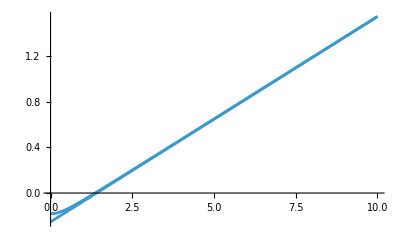

```mathematica
Integrate[σ^3/π^(3/2)Exp[-σ^2(r^2+rp^2-2*r*rp*Cos[θ])](-3/4 Cij(b*rp+c))*Sin[θ]*2π*rp^2,{θ,0,π}]
Integrate[%,{rp,0,Infinity}]//Simplify
Plot[{%,-3/4 Cij(b*r+c)}/.{b->0.18,c->-0.253,σ->2.853,Cij->-4/3},{r,0,10}]
```

-(3 Cij ⅇ^(-(r+rp)^2 σ^2) (-1+ⅇ^(4 r rp σ^2)) rp (c+(b-b ⅇ^(-rp μ))/μ) σ)/(4 √π r)

-1/(16 r μ (σ^2)^(3/2))3 Cij ⅇ^(-r μ) σ (4 ⅇ^(r μ) r (b+c μ) σ^2+b ⅇ^(μ^2/(4 σ^2)) (μ-2 r σ^2) Erfc[(μ-2 r σ^2)/(2 √(σ^2))]-b ⅇ^(1/4 μ (8 r+μ/σ^2)) (μ+2 r σ^2) Erfc[(μ+2 r σ^2)/(2 √(σ^2))])

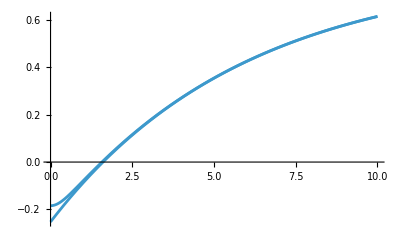

```mathematica
Integrate[σ^3/π^(3/2)Exp[-σ^2(r^2+rp^2-2*r*rp*Cos[θ])](-3/4 Cij(b*(1-Exp[-μ*rp])/μ+c))*Sin[θ]*2π*rp^2,{θ,0,π}]
Integrate[%,{rp,0,Infinity}]//Simplify
Plot[{%,-3/4 Cij(b*(1-Exp[-μ*r])/μ+c)}/.{b->0.18,c->-0.253,σ->2.853,μ->0.169,Cij->-4/3},{r,0,10}]
```

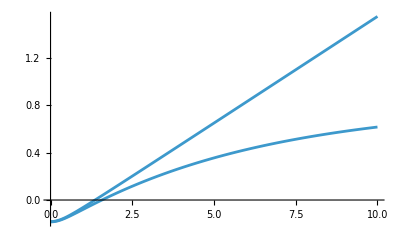

```mathematica
Plot[{-1/(16 r μ (σ^2)^(3/2))3 Cij ⅇ^(-r μ) σ (4 ⅇ^(r μ) r (b+c μ) σ^2+b ⅇ^(μ^2/(4 σ^2)) (μ-2 r σ^2) Erfc[(μ-2 r σ^2)/(2 √(σ^2))]-b ⅇ^(1/4 μ (8 r+μ/σ^2)) (μ+2 r σ^2) Erfc[(μ+2 r σ^2)/(2 √(σ^2))]),-(3 Cij (2 r σ ((b ⅇ^(-r^2 σ^2))/(√π)+c √(σ^2))+(b+2 b r^2 σ^2) Erf[r σ]))/(8 r σ^2)}/.{b->0.18,c->-0.253,σ->2.853,μ->0.169,Cij->-4/3},{r,0,10}]
```

```mathematica
Integrate[σ^3/π^(3/2)Exp[-σ^2(r^2+rp^2-2*r*rp*Cos[θ])](-3/4 Cij(b1*(1-Exp[-μ*rp])/μ))*Sin[θ]*2π*rp^2,{θ,0,π}]
screen1=Integrate[%,{rp,0,Infinity}]//Simplify
```

-(3 b1 Cij ⅇ^(-rp μ-(r+rp)^2 σ^2) (-1+ⅇ^(rp μ)) (-1+ⅇ^(4 r rp σ^2)) rp σ)/(4 √π r μ)

-(3 b1 Cij ⅇ^(-r μ) σ (4 ⅇ^(r μ) r σ^2+ⅇ^(μ^2/(4 σ^2)) (μ-2 r σ^2) Erfc[(μ-2 r σ^2)/(2 √(σ^2))]-ⅇ^(1/4 μ (8 r+μ/σ^2)) (μ+2 r σ^2) Erfc[(μ+2 r σ^2)/(2 √(σ^2))]))/(16 r μ (σ^2)^(3/2))

```mathematica
Integrate[σ^3/π^(3/2)Exp[-σ^2(r^2+rp^2-2*r*rp*Cos[θ])](-3/4 Cij(b2*(1-Exp[-μ*rp^2])/μ))*Sin[θ]*2π*rp^2,{θ,0,π}]
screen2=Integrate[%,{rp,0,Infinity}]//Simplify
```

-(3 b2 Cij ⅇ^(-rp^2 μ-(r+rp)^2 σ^2) (-1+ⅇ^(rp^2 μ)) (-1+ⅇ^(4 r rp σ^2)) rp σ)/(4 √π r μ)

-(3 b2 Cij σ (1/(√(σ^2))-(ⅇ^(-(r^2 μ σ^2)/(μ+σ^2)) σ^2)/((μ+σ^2)^(3/2))))/(4 μ)

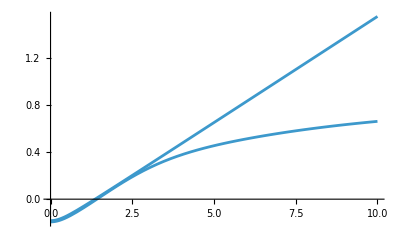

```mathematica
Plot[{screen1+screen2-3/4 Cij*c,-(3 Cij (2 r σ ((b ⅇ^(-r^2 σ^2))/(√π)+c √(σ^2))+(b+2 b r^2 σ^2) Erf[r σ]))/(8 r σ^2)}
/.{b->0.18,b1->0.14,b2->0.04,c->-0.253,σ->2.853,μ->0.169,Cij->-4/3},{r,0,10}]
```

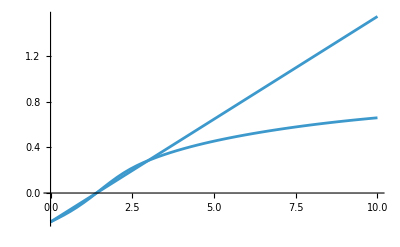

```mathematica
Plot[{-3/4 Cij(b1*(1-Exp[-μ*r^1])/μ)-3/4 Cij(b2*(1-Exp[-μ*r^2])/μ)-3/4 Cij(b3*(1-Exp[-μ*r^3])/μ)-3/4 Cij*c,-3/4 Cij*b*r-3/4 Cij*c}
/.{b->0.18,b1->0.14,b2->0.02,b3->0.02,c->-0.253,σ->2.853,μ->0.169,Cij->-4/3},{r,0,10}]
```